Ancillary file of the paper “Tidal Love numbers and quasi-normal modes of the Schwarzschild-Hernquist black hole”
by Sumanta Chakraborty, Geoffrey Compère and Ludovico Machet. 

This notebook was written by G . Compère with contributions from S. Chakraborty and L. Machet.

## 1. Axial TLN for the non-relativistic Hernquist profile (Up case)

equation for h0^1 :

```mathematica
eq=h0''[r]-(6r-4MBH)/(r^2(r-2MBH))h0[r]-C1 2rs r/(r+rs)^3 (4r^2+r(9rs+2MBH)-2MBH(7rs+6MBH));
```

```mathematica
Complexsol=h0[r]/.DSolve[eq== 0,h0[r],r][[1]]//Simplify;
```

Choice of other branch of Log to get a real solution:

```mathematica
Log[2 MBH-r]-> Log[r-2MBH]Log[-1]
```

Log[2 MBH-r]→ⅈ π Log[-2 MBH+r]

```mathematica
sol=Complexsol/.Log[2 MBH-r]-> Log[r-2MBH];
```

Check that it is a  solution:

```mathematica
eq/.{h0[r]-> sol,h0''[r]-> D[sol,r,r]}//Simplify
```

0

Schwarzschild case:

```mathematica
sol/.{C1-> 0}
```

(24 r^3 (-2 MBH+r) C[1]+(C[2] (2 MBH (2 MBH^3+2 MBH^2 r+3 MBH r^2-3 r^3)+3 r^3 (-2 MBH+r) Log[r]+3 (2 MBH-r) r^3 Log[-2 MBH+r]))/MBH^5)/(24 r)

h0[r] is regular at the horizon:

```mathematica
Series[sol,{r,2MBH,0}]
```

-1/(4 MBH^2)(32 C1 MBH^4 rs+232 C1 MBH^3 rs^2+156 C1 MBH^2 rs^3-50 C1 MBH rs^4-37 C1 rs^5+C[2]-144 C1 MBH^3 rs^2 Log[2 MBH+rs]-360 C1 MBH^2 rs^3 Log[2 MBH+rs]-264 C1 MBH rs^4 Log[2 MBH+rs]-60 C1 rs^5 Log[2 MBH+rs])+O[r-2 MBH]^1

h0’[r] is regular at the horizon only after fixing c2 :

```mathematica
pole=D[Series[D[sol,r],{r,2MBH,0}],r]
```

1/(2 MBH^3 (r-2 MBH))(-32 C1 MBH^4 rs-232 C1 MBH^3 rs^2-156 C1 MBH^2 rs^3+50 C1 MBH rs^4+37 C1 rs^5-C[2]+144 C1 MBH^3 rs^2 Log[2 MBH+rs]+360 C1 MBH^2 rs^3 Log[2 MBH+rs]+264 C1 MBH rs^4 Log[2 MBH+rs]+60 C1 rs^5 Log[2 MBH+rs])+O[r-2 MBH]^0

```mathematica
solc2=Solve[Normal[pole]== 0,C[2]][[1]]//Simplify
```

{C[2]→-C1 rs (2 MBH+rs) (16 MBH^3+108 MBH^2 rs+24 MBH rs^2-37 rs^3-12 rs (6 MBH^2+12 MBH rs+5 rs^2) Log[2 MBH+rs])}

Regular solution where we do not change the definition of C1.

```mathematica
solReg=sol/.solc2;
```

The solution is real

```mathematica
N[solReg/.{rs-> 100,r-> 8,MBH-> 1}]
```

0.00520833 (5.27951×10^14 C1+73728. C[1])

Expansion of h0[r] at infinity.

```mathematica
$Assumptions={R>0,rs>0,MBH>0};
```

```mathematica
Coefr3=1/R^3Normal[Series[solReg,{r,∞,-3}]]/.{r-> R}
```

1/(12 MBH^5)(52 C1 MBH^4 rs+50 C1 MBH^3 rs^2+9 C1 MBH^2 rs^3+12 MBH^5 C[1]-108 C1 MBH^3 rs^2 Log[rs]^2-270 C1 MBH^2 rs^3 Log[rs]^2-198 C1 MBH rs^4 Log[rs]^2-45 C1 rs^5 Log[rs]^2+108 C1 MBH^3 rs^2 Log[2 MBH+rs]^2+270 C1 MBH^2 rs^3 Log[2 MBH+rs]^2+198 C1 MBH rs^4 Log[2 MBH+rs]^2+45 C1 rs^5 Log[2 MBH+rs]^2)

```mathematica
Coefrm2= Coefficient[Series[solReg,{r,∞,2}] r^3,r]/.{r-> R}
```

1/25 (324 C1 MBH^3 rs^2+270 C1 MBH^2 rs^3-196 C1 MBH rs^4-125 C1 rs^5+720 C1 MBH^3 rs^2 Log[R]+1800 C1 MBH^2 rs^3 Log[R]+1320 C1 MBH rs^4 Log[R]+300 C1 rs^5 Log[R]-720 C1 MBH^3 rs^2 Log[2 MBH+rs]-1800 C1 MBH^2 rs^3 Log[2 MBH+rs]-1320 C1 MBH rs^4 Log[2 MBH+rs]-300 C1 rs^5 Log[2 MBH+rs])

```mathematica
Love=Simplify[-ϵ Coefrm2/3/C1/R^5]
```

-1/(75 R^5)rs^2 (2 MBH+rs) ϵ (162 MBH^2+54 MBH rs-125 rs^2+60 (6 MBH^2+12 MBH rs+5 rs^2) Log[R]-60 (6 MBH^2+12 MBH rs+5 rs^2) Log[2 MBH+rs])

```mathematica
kBUp =FullSimplify@Normal@Series[Love/.{MBH-> η rs},{η,0,0}]/.{ϵ-> MDM/rs}
```

(MDM rs^4 (5-12 Log[R]+12 Log[rs]))/(3 R^5)

```mathematica
N[Love/.{MBH-> 100,rs-> 200000,R-> 100}]
```

1.02856×10^18 ϵ

## 2. Axial TLN for the non-relativistic Hernquist profile (Down case)

equation for h0^1 :

```mathematica
eq=h0''[r]-(6r-4MBH)/(r^2(r-2MBH))h0[r]-C1 2rs r/(r+rs)^3 (4r^2+r(5rs-6MBH)-8rs MBH);
```

```mathematica
Complexsol=h0[r]/.DSolve[eq== 0,h0[r],r][[1]]//Simplify;
```

Choice of other branch of Log to get a real solution:

```mathematica
Log[2 MBH-r]-> Log[r-2MBH]Log[-1]
```

Log[2 MBH-r]→ⅈ π Log[-2 MBH+r]

```mathematica
sol=Complexsol/.Log[2 MBH-r]-> Log[r-2MBH];
```

Check that it is a  solution:

```mathematica
eq/.{h0[r]-> sol,h0''[r]-> D[sol,r,r]}//Simplify
```

0

Schwarzschild case:

```mathematica
sol/.{C1-> 0}
```

(24 r^3 (-2 MBH+r) C[1]+(C[2] (2 MBH (2 MBH^3+2 MBH^2 r+3 MBH r^2-3 r^3)+3 r^3 (-2 MBH+r) Log[r]+3 (2 MBH-r) r^3 Log[-2 MBH+r]))/MBH^5)/(24 r)

h0[r] is regular at the horizon:

```mathematica
Series[sol,{r,2MBH,0}]
```

-1/(12 MBH^2)(16 C1 MBH^4 rs-64 C1 MBH^3 rs^2-252 C1 MBH^2 rs^3-120 C1 MBH rs^4-3 C1 rs^5+3 C[2]+144 C1 MBH^2 rs^3 Log[2 MBH+rs]+192 C1 MBH rs^4 Log[2 MBH+rs]+60 C1 rs^5 Log[2 MBH+rs])+O[r-2 MBH]^1

h0’[r] is regular at the horizon only after fixing c2 :

```mathematica
pole=D[Series[D[sol,r],{r,2MBH,0}],r]
```

1/(6 MBH^3 (r-2 MBH))(-16 C1 MBH^4 rs+64 C1 MBH^3 rs^2+252 C1 MBH^2 rs^3+120 C1 MBH rs^4+3 C1 rs^5-3 C[2]-144 C1 MBH^2 rs^3 Log[2 MBH+rs]-192 C1 MBH rs^4 Log[2 MBH+rs]-60 C1 rs^5 Log[2 MBH+rs])+O[r-2 MBH]^0

```mathematica
solc2=Solve[Normal[pole]== 0,C[2]][[1]]//Simplify
```

{C[2]→-1/3 C1 rs (16 MBH^4-64 MBH^3 rs-252 MBH^2 rs^2-120 MBH rs^3-3 rs^4+12 rs^2 (12 MBH^2+16 MBH rs+5 rs^2) Log[2 MBH+rs])}

Regular solution where we do not change the definition of C1.

```mathematica
solReg=sol/.solc2;
```

The solution is real

```mathematica
N[solReg/.{rs-> 100,r-> 8,MBH-> 1}]
```

0.00520833 (-1.74051×10^14 C1+73728. C[1])

Expansion of h0[r] at infinity.

```mathematica
$Assumptions={R>0,rs>0,MBH>0};
```

```mathematica
Coefr3=1/R^3Normal[Series[solReg,{r,∞,-3}]]/.{r-> R}
```

1/(36 MBH^5)(-32 C1 MBH^4 rs-160 C1 MBH^3 rs^2-81 C1 MBH^2 rs^3+36 MBH^5 C[1]+108 C1 MBH^2 rs^3 Log[rs]^2+144 C1 MBH rs^4 Log[rs]^2+45 C1 rs^5 Log[rs]^2-108 C1 MBH^2 rs^3 Log[2 MBH+rs]^2-144 C1 MBH rs^4 Log[2 MBH+rs]^2-45 C1 rs^5 Log[2 MBH+rs]^2)

```mathematica
Coefrm2= Coefficient[Series[solReg,{r,∞,2}] r^3,r]/.{r-> R}
```

1/25 (-108 C1 MBH^2 rs^3-114 C1 MBH rs^4-25 C1 rs^5-240 C1 MBH^2 rs^3 Log[R]-320 C1 MBH rs^4 Log[R]-100 C1 rs^5 Log[R]+240 C1 MBH^2 rs^3 Log[2 MBH+rs]+320 C1 MBH rs^4 Log[2 MBH+rs]+100 C1 rs^5 Log[2 MBH+rs])

```mathematica
Love=Simplify[-ϵ Coefrm2/3/C1/R^5]
```

(rs^3 ϵ (108 MBH^2+114 MBH rs+25 rs^2+20 (12 MBH^2+16 MBH rs+5 rs^2) Log[R]-20 (12 MBH^2+16 MBH rs+5 rs^2) Log[2 MBH+rs]))/(75 R^5)

```mathematica
kBDown = Normal@Series[Love/.{MBH-> η rs},{η,0,0}]/.{ϵ-> MDM/rs}
```

(MDM rs^4 (1+4 Log[R]-4 Log[rs]))/(3 R^5)

```mathematica
Simplify[(kBUp-kBDown)/kBUp]
```

(4-16 Log[R]+16 Log[rs])/(5-12 Log[R]+12 Log[rs])

## 3. Axial TLN for the relativistic Schwarzschild-Hernquist profile (Up case)

### 3.1. Equation (valid for all regions)

```mathematica
AVal=1;
(* 
Overall scaling, set to 1 for numerical evaluations, factor A reintroduced at the end 
*)
```

equation for h0^1 :

```mathematica
xsp=2 rs MDM/MBH^2;
```

```mathematica
ρ=λ A (1- 4/x)^w x^(-q)(*(1+x/xsp)^(q-4)*)/.{x-> r/MBH}
```

A (1-(4 MBH)/r)^w (r/MBH)^-q λ

```mathematica
mmBare = 4 π Integrate[(r)^2 ρ,r]
```

(4 A MBH^q π r^(3-q) λ Hypergeometric2F1[-3+q,-w,-2+q,(4 MBH)/r])/(3-q)

```mathematica
mm=mmBare-(mmBare/.{r-> 4 MBH})+MBH
```

MBH-(4^(4-q) A MBH^3 π λ Gamma[-2+q] Gamma[1+w])/((3-q) Gamma[-2+q+w])+(4 A MBH^q π r^(3-q) λ Hypergeometric2F1[-3+q,-w,-2+q,(4 MBH)/r])/(3-q)

```mathematica
gg=1-2 mm/r;
pt = mm ρ/(r-2 mm)/2;
```

```mathematica
eqh=gg h0''[r]-4 π r ρ h0'[r]-(4/r^2+2 gg/r^2 +8 π (ρ+2 pt) )h0[r]/.{h0-> Function[{r},h00[r]+λ h01[r]]};
```

```mathematica
Series[eqh,{λ,0,0}]
```

((2 (2 MBH-3 r) h00[r])/r^3+(1-(2 MBH)/r) h00''[r])+O[λ]^1

```mathematica
eq=1/λ Simplify[1/(1-(2 MBH)/r)Normal@Series[eqh,{λ,0,1}]/.{h00-> Function[{r},C1 r^2(r-2MBH)]}]/.{h01-> h0}
```

((-4 MBH+6 r) h0[r])/((2 MBH-r) r^2)+(4 A C1 π r (2^(9-2 q) MBH^3 Gamma[-2+q] Gamma[1+w]-MBH^q r^(2-q) Gamma[-2+q+w] ((-3+q) (1-(4 MBH)/r)^w (6 MBH-5 r)+8 r Hypergeometric2F1[-3+q,-w,-2+q,(4 MBH)/r])))/((-3+q) (2 MBH-r) Gamma[-2+q+w])+h0''[r]

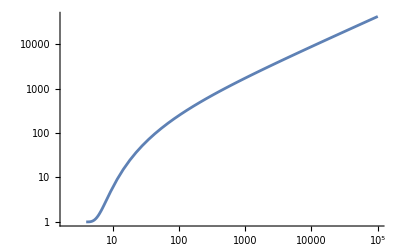

```mathematica
LogLogPlot[mm/.{q-> 233/100,w-> 245/100,MBH-> 1,λ->1,A->1},{r,2,10^5}]
```

### 3.2. Near zone (numerical solution)

```mathematica
rsVal=SetPrecision[20 10^3 3.086 10^16 /2900 MBH,100];
```

```mathematica
GenMatchingNear[h0p_]:=Module[{SolNear},
SolNear=h0[r]/. Block[{MBH= 1,MDM=10^12,rs=rsVal,λ=1,A =AVal,C1= 1,q=233/100,w=245/100},
(*NDSolve[{eq==0,h0[4 MBH]== 0,h0'[4 MBH]== h0p},h0[r],{r,4,10^16},WorkingPrecision->2$MachinePrecision][[1]]*)
rin=4(1+1/100);
NDSolve[{eq==0,h0[rin]== 0,h0'[rin]== h0p},h0[r],{r,rin,10^10},WorkingPrecision->3.5$MachinePrecision][[1]]];
MatchingValueNear[thisr_]:= SolNear/.{r-> thisr};
DSolNearFunction= D[SolNear,r];
MatchingValueDNear[thisr_]:= DSolNearFunction/.{r-> thisr};
]
```

```mathematica
GenMatchingNear[0]
```

### 3.3. Far zone (asymptotic series)

```mathematica
DSolve[0== eq/.{C1-> 0},h0[r],r][[1]]/.{MBH-> 1}
```

{h0[r]→(-2+r) r^2 C[1]+(C[2] (4+4 r+6 r^2-6 r^3+6 r^3 Log[-2+r]-3 r^4 Log[-2+r]-6 r^3 Log[r]+3 r^4 Log[r]))/(24 r)}

```mathematica
Series[(C[2] (4+4 r+6 r^2-6 r^3+6 r^3 Log[-2+r]-3 r^4 Log[-2+r]-6 r^3 Log[r]+3 r^4 Log[r]))/(24 r),{r,Infinity,2}]
```

-C[2]/(5 r^2)+O[1/r]^3

#### Asymptotic series determination

```mathematica
nmax=25;
```

```mathematica
Ansatz[r_]:=r^a(Sum[cc[i]/r^i,{i,0,nmax-2}])+cc[nmax-1] r^3+cc[nmax]/r^2;
```

```mathematica
solcoeff=eq/.{q-> 233/100,w-> 245/100,MBH-> 1,h0-> Function[{r},Ansatz[r]+(-2+r) r^2 C[1]+1/(24 r)C[2] (4+4 r+6 r^2-6 r^3+6 r^3 Log[-2+r]-3 r^4 Log[-2+r]-6 r^3 Log[r]+3 r^4 Log[r])]};
```

```mathematica
Tabcoeffs=Quiet@DeleteDuplicates[Select[Series[solcoeff,{r,∞,nmax}]/.(a->2+67/100),FreeQ[r]][[2]]];
```

```mathematica
(*Tabcoeffs[[1]]*)
```

```mathematica
solcoeffs=Solve[Tabcoeffs==Table[0,Length@Tabcoeffs],Table[cc[i],{i,0,nmax}]][[1]];
```

```mathematica
Series[solcoeff,{r,∞,nmax}]/.a->2+67/100/.solcoeffs//Simplify
```

O[1/r]^(2333/100)

```mathematica
solh0Far= Function[{r}, Ansatz[r]+(-2+r) r^2 C[1]+1/(24 r)C[2] (4+4 r+6 r^2-6 r^3+6 r^3 Log[-2+r]-3 r^4 Log[-2+r]-6 r^3 Log[r]+3 r^4 Log[r])/.a->2+67/100/.solcoeffs];
```

```mathematica
sol=eq//.{q-> 233/100,w-> 245/100,MBH->1,h0-> solh0Far};
```

```mathematica
Simplify@Series[sol,{r,∞,nmax-2}]
```

O[1/r]^(2301/100)

```mathematica
MatchingValueFar[thisr_]:=Block[{q=233/100,w=245/100,MBH=1,A=AVal,C1=1},solh0Far[r]]/.{r-> thisr}
```

```mathematica
DFarFunction=Block[{q=233/100,w=245/100,MBH=1,A=AVal,C1=1},D[solh0Far[r],r]];
```

```mathematica
MatchingValueDFar[thisr_]:=DFarFunction/.{r-> thisr}
```

### 3.4. Matching and Love number

```mathematica
solc1[r_]:=Module[{},Solve[N[{MatchingValueFar[r]== MatchingValueNear[r],MatchingValueDFar[r]== MatchingValueDNear[r]},100],{C[1],C[2]}][[1]]]
```

```mathematica
NormalizationOdd= -3;
```

```mathematica
A MBH^7 LoveUpRel/. Solve[C[2]==  NormalizationOdd LoveUpRel  R^5,LoveUpRel ][[1]]
```

-(A MBH^7 C[2])/(3 R^5)

```mathematica
GenMatchingNear[0];
C[2]/.solc1[10]
```

839.58168234744353373042534440111454478249949597640526

```mathematica
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[10]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[100]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[250]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[300]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[500]
```

-(279.860560782481177910141781467038181594166498658801753 A MBH^7)/R^5

-(279.860558557026473759957193331642203450424771261953249 A MBH^7)/R^5

-(279.86060025327009066609578752219871828616269142760752 A MBH^7)/R^5

-(279.860436936428987555436846909758186740307716962759159 A MBH^7)/R^5

-(279.85354523280667044430848286169407400536561646813999 A MBH^7)/R^5

```mathematica
TLN[rmatch_]:=-(A MBH^7 C[2])/(3 R^5)/.solc1[rmatch];
```

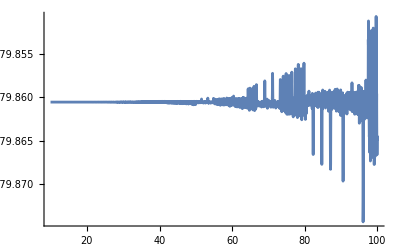

```mathematica
Plot[TLN[x]/.{A->1,MBH->1,R->1},{x,10,100},PlotRange->All]
```

## 4. Axial TLN for the relativistic Schwarzschild-Hernquist profile (Down case)

### 3.1. Equation (valid for all regions)

```mathematica
AVal=1;
(* 
Overall scaling, set to 1 for numerical evaluations, factor A reintroduced at the end 
*)
```

equation for h0^1 :

```mathematica
xsp=2 rs MDM/MBH^2;
```

```mathematica
ρ=λ A (1- 4/x)^w x^(-q)(*(1+x/xsp)^(q-4)*)/.{x-> r/MBH}
```

A (1-(4 MBH)/r)^w (r/MBH)^-q λ

```mathematica
mmBare = 4 π Integrate[(r)^2 ρ,r]
```

(4 A MBH^q π r^(3-q) λ Hypergeometric2F1[-3+q,-w,-2+q,(4 MBH)/r])/(3-q)

```mathematica
mm=mmBare-(mmBare/.{r-> 4 MBH})+MBH
```

MBH-(4^(4-q) A MBH^3 π λ Gamma[-2+q] Gamma[1+w])/((3-q) Gamma[-2+q+w])+(4 A MBH^q π r^(3-q) λ Hypergeometric2F1[-3+q,-w,-2+q,(4 MBH)/r])/(3-q)

```mathematica
gg=1-2 mm/r;
pt = mm ρ/(r-2 mm)/2;
```

```mathematica
eqh=gg h0''[r]-4π r ρ h0'[r]-(4/r^2+2gg/r^2-8π(+ρ))h0[r]/.{h0-> Function[{r},h00[r]+λ h01[r]]};
```

```mathematica
Series[eqh,{λ,0,0}]
```

((2 (2 MBH-3 r) h00[r])/r^3+(1-(2 MBH)/r) h00''[r])+O[λ]^1

```mathematica
eq=1/λ Simplify[1/(1-(2 MBH)/r)Normal@Series[eqh,{λ,0,1}]/.{h00-> Function[{r},C1 r^2(r-2MBH)]}]/.{h01-> h0}
```

((-4 MBH+6 r) h0[r])/((2 MBH-r) r^2)+(4 A C1 π r (2^(9-2 q) MBH^3 Gamma[-2+q] Gamma[1+w]+MBH^q r^(3-q) Gamma[-2+q+w] ((-3+q) (1-(4 MBH)/r)^w-8 Hypergeometric2F1[-3+q,-w,-2+q,(4 MBH)/r])))/((-3+q) (2 MBH-r) Gamma[-2+q+w])+h0''[r]

```mathematica
LogLogPlot[mm/.{q-> 233/100,w-> 245/100,MBH-> 1,λ->1,A->1},{r,2,10^5}]
```

-Graphics-

### 3.2. Near zone (numerical solution)

```mathematica
rsVal=SetPrecision[20 10^3 3.086 10^16 /2900 MBH,100];
```

```mathematica
GenMatchingNear[h0p_]:=Module[{SolNear},
SolNear=h0[r]/. Block[{MBH= 1,MDM=10^12,rs=rsVal,λ=1,A =AVal,C1= 1,q=233/100,w=245/100},
(*NDSolve[{eq==0,h0[4 MBH]== 0,h0'[4 MBH]== h0p},h0[r],{r,4,10^16},WorkingPrecision->2$MachinePrecision][[1]]*)
rin=4(1+1/100);
NDSolve[{eq==0,h0[rin]== 0,h0'[rin]== h0p},h0[r],{r,rin,10^10},WorkingPrecision->3.5$MachinePrecision][[1]]];
MatchingValueNear[thisr_]:= SolNear/.{r-> thisr};
DSolNearFunction= D[SolNear,r];
MatchingValueDNear[thisr_]:= DSolNearFunction/.{r-> thisr};
]
```

```mathematica
GenMatchingNear[0]
```

### 3.3. Far zone (asymptotic series)

```mathematica
DSolve[0== eq/.{C1-> 0},h0[r],r][[1]]/.{MBH-> 1}
```

{h0[r]→(-2+r) r^2 C[1]+(C[2] (4+4 r+6 r^2-6 r^3+6 r^3 Log[-2+r]-3 r^4 Log[-2+r]-6 r^3 Log[r]+3 r^4 Log[r]))/(24 r)}

#### Asymptotic series determination

```mathematica
nmax=25;
```

```mathematica
Ansatz[r_]:=r^a(Sum[cc[i]/r^i,{i,0,nmax-2}])+cc[nmax-1] r^3+cc[nmax]/r^2;
```

```mathematica
solcoeff=eq/.{q-> 233/100,w-> 245/100,MBH-> 1,h0-> Function[{r},Ansatz[r]+(-2+r) r^2 C[1]+1/(24 r)C[2] (4+4 r+6 r^2-6 r^3+6 r^3 Log[-2+r]-3 r^4 Log[-2+r]-6 r^3 Log[r]+3 r^4 Log[r])]};
```

```mathematica
Normal@Series[solcoeff,{r,∞,nmax}]//Simplify;
```

```mathematica
Tabcoeffs=Quiet@DeleteDuplicates[Select[Series[solcoeff,{r,∞,nmax}]/.a->2+67/100,FreeQ[r]][[2]]];
```

```mathematica
solcoeffs=Solve[Tabcoeffs==Table[0,Length@Tabcoeffs],Table[cc[i],{i,0,nmax}]][[1]];
```

```mathematica
Series[solcoeff,{r,∞,nmax}]/.a->2+67/100/.solcoeffs//Simplify
```

O[1/r]^(2333/100)

```mathematica
solh0Far= Function[{r}, Ansatz[r]+(-2+r) r^2 C[1]+1/(24 r)C[2] (4+4 r+6 r^2-6 r^3+6 r^3 Log[-2+r]-3 r^4 Log[-2+r]-6 r^3 Log[r]+3 r^4 Log[r])/.a->2+67/100/.solcoeffs];
```

```mathematica
sol=eq//.{q-> 233/100,w-> 245/100,MBH->1,h0-> solh0Far};
```

```mathematica
Simplify@Series[sol,{r,∞,nmax-2}]
```

O[1/r]^(2301/100)

```mathematica
MatchingValueFar[thisr_]:=Block[{q=233/100,w=245/100,MBH=1,A=AVal,C1=1},solh0Far[r]]/.{r-> thisr}
```

```mathematica
DFarFunction=Block[{q=233/100,w=245/100,MBH=1,A=AVal,C1=1},D[solh0Far[r],r]];
```

```mathematica
MatchingValueDFar[thisr_]:=DFarFunction/.{r-> thisr}
```

### 3.4. Matching and Love number

```mathematica
solc1[r_]:=Module[{},Solve[N[{MatchingValueFar[r]== MatchingValueNear[r],MatchingValueDFar[r]== MatchingValueDNear[r]},100],{C[1],C[2]}][[1]]]
```

```mathematica
NormalizationOdd= -3;
```

```mathematica
A MBH^7 LoveUpRel/. Solve[C[2]==  NormalizationOdd LoveUpRel  R^5,LoveUpRel ][[1]]
```

-(A MBH^7 C[2])/(3 R^5)

```mathematica
GenMatchingNear[0];
C[2]/.solc1[10]
```

306.215223540911028056590883094088257042504122129188768

```mathematica
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[10]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[100]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[300]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[500]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[1000]
```

-(102.071741180303676018863627698029419014168040709729589 A MBH^7)/R^5

-(102.07174118350047679348449361869032530696555893741832 A MBH^7)/R^5

-(102.07222580805822575735807068759471391539948975455684 A MBH^7)/R^5

-(102.070424416144785929753722017430076923134628184312163 A MBH^7)/R^5

-(102.11675241200417055153041496251955565585427741559379 A MBH^7)/R^5

```mathematica
TLN[rmatch_]:=-(A MBH^7 C[2])/(3 R^5)/.solc1[rmatch];
```

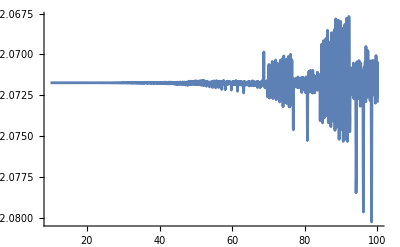

```mathematica
Plot[TLN[x]/.{A->1,MBH->1,R->1},{x,10,100},PlotRange->All]
```

## 5. Polar TLN for the relativistic Schwarzschild-Hernquist profile

### 5.1 Equation - valid for all regions

```mathematica
AVal=1;
(* 
Overall scaling, set to 1 for numerical evaluations, factor A reintroduced at the end 
*)
```

equation for h0^1 :

```mathematica
xsp=2 rs MDM/MBH^2;
```

```mathematica
ρ=λ A (1- 4/x)^w x^(-q)(*(1+x/xsp)^(q-4)*)/.{x-> r/MBH}
```

A (1-(4 MBH)/r)^w (r/MBH)^-q λ

```mathematica
mmBare = 4 π Integrate[(r)^2 ρ,r]
```

(4 A MBH^q π r^(3-q) λ Hypergeometric2F1[-3+q,-w,-2+q,(4 MBH)/r])/(3-q)

```mathematica
mm=mmBare-(mmBare/.{r-> 4 MBH})+MBH
```

MBH-(4^(4-q) A MBH^3 π λ Gamma[-2+q] Gamma[1+w])/((3-q) Gamma[-2+q+w])+(4 A MBH^q π r^(3-q) λ Hypergeometric2F1[-3+q,-w,-2+q,(4 MBH)/r])/(3-q)

```mathematica
gg=1-2 mm/r;
pt = mm ρ/(r-2 mm)/2;
```

```mathematica
eqh= H''[r]+((1+gg)/r/gg+16 π r pt/(1-gg)+4π r(1-3 gg)ρ/gg/(gg-1))H'[r]+(-(1+(l+2)(l-1)gg+gg^2)/r^2/gg^2 +32π pt/gg+16π ρ/gg/(1-gg))H[r]/.{l->2};
```

```mathematica
Series[eqh,{λ,0,0}]
```

(-(2 (2 MBH^2-6 MBH r+3 r^2) H[r])/((2 MBH-r)^2 r^2)+(2 (MBH-r) H'[r])/((2 MBH-r) r)+H''[r])+O[λ]^1

```mathematica
eq= Simplify[1/λ Normal@Series[eqh/.{H-> Function[{r},H0[r]+λ h0[r]]},{λ,0,1}]/.{H0-> Function[{r},C1 ((-2 MBH+r) r)/MBH^2]}]
```

1/(r^2 (-2 MBH+r)^2)((4^(5-q) A C1 MBH π (3 MBH-2 r) r^2 Gamma[-2+q] Gamma[1+w])/((-3+q) Gamma[-2+q+w])-2 (2 MBH^2-6 MBH r+3 r^2) h0[r]+1/(-3+q)8 A C1 MBH^(-3+q) π r^(4-q) (-((-3+q) (1-(4 MBH)/r)^w (8 MBH^3-14 MBH^2 r+9 MBH r^2-2 r^3))+2 MBH r (-3 MBH+2 r) Hypergeometric2F1[-3+q,-w,-2+q,(4 MBH)/r])+2 r (2 MBH^2-3 MBH r+r^2) h0'[r]+r^2 (-2 MBH+r)^2 h0''[r])

```mathematica
-(2 (2 MBH^2-6 MBH r+3 r^2) H[r])/((2 MBH-r)^2 r^2)+(2 (MBH-r) H'[r])/((2 MBH-r) r)+H''[r]/.{H-> Function[{r},C1 ((-2 MBH+r) r)/MBH^2]}//Simplify
```

0

### 5.2. Near zone (numerical solution)

```mathematica
rsVal=SetPrecision[20 10^3 3.086 10^16 /2900 MBH,100];
```

```mathematica
GenMatchingNear[h0p_]:=Module[{SolNear},
SolNear=h0[r]/. Block[{MBH= 1,MDM=10^12,rs=rsVal,λ=1,A =AVal,C1= 1,q=233/100,w=245/100},
(*NDSolve[{eq==0,h0[4 MBH]== 0,h0'[4 MBH]== h0p},h0[r],{r,4,10^16},WorkingPrecision->2$MachinePrecision][[1]]*)
rin=4(1+1/100);
NDSolve[{eq==0,h0[rin]== 0,h0'[rin]== h0p},h0[r],{r,rin,10^10},WorkingPrecision->3.5$MachinePrecision][[1]]];
MatchingValueNear[thisr_]:= SolNear/.{r-> thisr};
DSolNearFunction= D[SolNear,r];
MatchingValueDNear[thisr_]:= DSolNearFunction/.{r-> thisr};
]
```

```mathematica
GenMatchingNear[0]
```

### 5.3. Far zone (asymptotic series)

```mathematica
$Assumptions=r>2&&r∈ Reals;
```

```mathematica
DSolve[0== eq/.{C1-> 0},h0[r],r][[1]]/.{MBH-> 1}//Simplify
```

{h0[r]→-3 (-2+r) r C[1]+(C[2] (4+8 r-18 r^2+6 r^3+3 (-2+r)^2 r^2 Log[2-r]-3 (-2+r)^2 r^2 Log[r]))/(2 (-2+r) r)}

```mathematica
Series[-3 (-2+r) r C[1]+(C[2] (4+8 r-18 r^2+6 r^3+3 (-2+r)^2 r^2 Log[2-r]-3 (-2+r)^2 r^2 Log[r]))/(2 (-2+r) r),{r,Infinity,4}]
```

(-3 C[1]+(3 ⅈ π C[2])/2) r^2+(6 C[1]-3 ⅈ π C[2]) r-(8 C[2])/(5 r^3)-(24 C[2])/(5 r^4)+O[1/r]^5

```mathematica
(*Shall we fix c1 so that the expansion is real?*)
```

```mathematica
(*Series[-3 (-2+r) r C[1]+(C[2] (4+8 r-18 r^2+6 r^3+3 (-2+r)^2 r^2 Log[2-r]-3 (-2+r)^2 r^2 Log[r]))/(2 (-2+r) r)/.C[1]->(ⅈ π C[2])/2,{r,Infinity,4}]*)
```

```mathematica
Solve[-3 C[1]+(3 ⅈ π C[2])/2==0,C[1]]
```

{{C[1]→(ⅈ π C[2])/2}}

```mathematica
(*h0[r]->-3 (-2+r) r C[1]+(C[2] (4+8 r-18 r^2+6 r^3+3 (-2+r)^2 r^2 Log[2-r]-3 (-2+r)^2 r^2 Log[r]))/(2 (-2+r) r)/.C[1]->(ⅈ π C[2])/2*)
```

#### Asymptotic series determination

```mathematica
nmax=25;
```

```mathematica
Ansatz[r_]:=r^a(Sum[cc[i]/r^i,{i,0,nmax-2}])+cc[nmax-1] r^2+cc[nmax]/r^3;
```

```mathematica
solcoeff=eq/.{q-> 233/100,w-> 245/100,MBH-> 1,h0-> Function[{r},Ansatz[r]-3 (-2+r) r C[1]+(C[2] (4+8 r-18 r^2+6 r^3+3 (-2+r)^2 r^2 Log[2-r]-3 (-2+r)^2 r^2 Log[r]))/(2 (-2+r) r)]};
```

```mathematica
Normal@Series[solcoeff,{r,∞,nmax}]//Simplify;
```

```mathematica
Tabcoeffs=Quiet@DeleteDuplicates[Select[Series[solcoeff,{r,∞,nmax}]/.a->2+67/100,FreeQ[r]][[2]]];
```

```mathematica
solcoeffs=Solve[Tabcoeffs==Table[0,Length@Tabcoeffs],Table[cc[i],{i,0,nmax}]][[1]];
```

```mathematica
Series[solcoeff,{r,∞,nmax}]/.a->2+67/100/.solcoeffs//Simplify
```

O[1/r]^(2333/100)

```mathematica
solh0Far= Function[{r}, Ansatz[r]-3 (-2+r) r C[1]+(C[2] (4+8 r-18 r^2+6 r^3+3 (-2+r)^2 r^2 Log[2-r]-3 (-2+r)^2 r^2 Log[r]))/(2 (-2+r) r)/.a->2+67/100/.solcoeffs];
```

```mathematica
sol=eq//.{q-> 233/100,w-> 245/100,MBH->1,h0-> solh0Far};
```

```mathematica
Simplify@Series[sol,{r,∞,nmax-2}]
```

O[1/r]^(2333/100)

```mathematica
MatchingValueFar[thisr_]:=Block[{q=233/100,w=245/100,MBH=1,A=AVal,C1=1},solh0Far[r]]/.{r-> thisr}
```

```mathematica
DFarFunction=Block[{q=233/100,w=245/100,MBH=1,A=AVal,C1=1},D[solh0Far[r],r]];
```

```mathematica
MatchingValueDFar[thisr_]:=DFarFunction/.{r-> thisr}
```

### 5.4. Matching and Love number

```mathematica
solc1[r_]:=Module[{},Chop@Solve[N[{MatchingValueFar[r]== MatchingValueNear[r],MatchingValueDFar[r]== MatchingValueDNear[r]},100],{C[1],C[2]}][[1]]]
```

```mathematica
solc1[10]
```

{C[1]→10.263500604969959780842405517997912038432112337579871-3043.78479548428230279396609020094866095017978668146453 ⅈ,C[2]→-1937.73358363710893234533492691072691241461717699489127}

```mathematica
(*Notice c1 is complex*)
```

```mathematica
NormalizationOdd= -3;
```

```mathematica
A MBH^7 LoveUpRel/. Solve[C[2]==  NormalizationOdd LoveUpRel  R^5,LoveUpRel ][[1]]
```

-(A MBH^7 C[2])/(3 R^5)

```mathematica
GenMatchingNear[0];
C[2]/.solc1[10]
```

-1937.73358363710893234533492691072691241461717699489127

```mathematica
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[10]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[100]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[300]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[500]
LoveUpVal =-(A MBH^7 C[2])/(3 R^5)/.solc1[1000]
```

(645.911194545702977448444975636908970804872392331630422 A MBH^7)/R^5

(645.911197024742650365406667710729723883173476921587 A MBH^7)/R^5

(645.90918140474763255438116452611904278398956345441 A MBH^7)/R^5

(645.90818179568124300909257698038591687180019858962 A MBH^7)/R^5

(644.314693921526319778255650224829481420700667248 A MBH^7)/R^5

```mathematica
TLN[rmatch_]:=-(A MBH^7 C[2])/(3 R^5)/.solc1[rmatch];
```

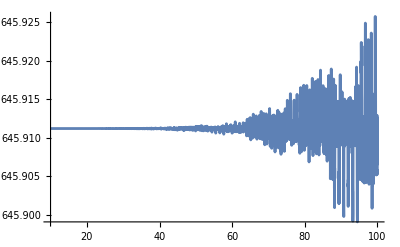

```mathematica
Plot[Re@TLN[x]/.{A->1,MBH->1,R->1},{x,10,100},PlotRange->All]
```